## The functions handling the evolution of programs

## BNF grammar rules

```mathematica
rules = {root -> Inactivate[listfunction[list, crit]],
		listfunction -> Inactivate[Select],
		list :> Inactivate[Table[RandomInteger[10], RandomInteger[10]]],
		list :> Inactivate[Table[expr, {x, 0, RandomInteger[{1, 10}]}]],
		expr :> Inactivate[x],
		expr :> Inactivate[const],
		expr :> expr+expr,
		expr :> expr-expr,
		expr :> expr*expr,
		expr :> expr/expr,
		const :> RandomReal[10],
		crit :> Inactivate[(puref > RandomInteger[1] &)],
		crit :> Inactivate[(puref < RandomInteger[20] &)],
		puref :> Inactivate[#],
		puref :> Inactivate[const],
		puref :> puref+puref,
		puref :> puref-puref,
		puref :> puref*puref,
		puref :> puref/puref};
```

## Random derivation tree

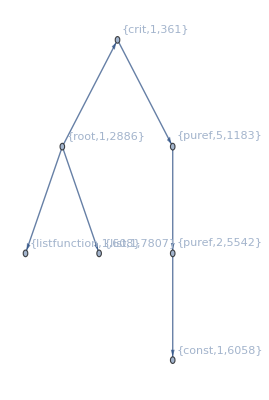

```mathematica
RandomDerivation[expr_, rules_, prev_, g_] :=
	Module[
		{keyList, list, index, new, node},
		keyList = Keys[Counts[Keys[rules]]];
		If[Length[Select[keyList, Length[Position[expr, #]] ≠ 0 &]] == 0, Return[g]];
		gr = g;
		keyList = Keys[Counts[Keys[rules]]];
		Map[
			With[
				{key = #},
				Map[
					With[
						{pos = #},
						list = Select[rules, #[[1]] == key &];
						index = RandomInteger[{1, Length[list]}];
						new = Last[list[[index]]];
						node = {key, index, RandomInteger[10000]};
						gr = EdgeAdd[gr, prev -> node];
						gr = RandomDerivation[new, rules, node, gr]
					]&,
					Position[expr, key]
				]
			]&,
			keyList
		];
		gr
	]
	
graph = RandomDerivation[root, rules, {root, 1, 0}, Graph[{}]];
graph = VertexDelete[graph, First[Select[VertexList[graph], VertexInDegree[graph, #] == 0 &]]];
Graph[graph, VertexLabels -> "Name"]
```

## Create program from derivation tree

```mathematica
CodeFromDerivation[derivGraph_, rules_] :=
	Module[
		{expr, expr2, keyList, pos, currentNodes2},
		expr = First[First[Select[VertexList[derivGraph], VertexInDegree[derivGraph, #] == 0 &]]];
		expr2 = expr;
		keyList = Keys[Counts[Keys[rules]]];
		NestWhile[
			With[
				{currentNodes = #},
				currentNodes2 = Flatten[Map[
					With[
						{node = #},
						Select[node /. #& /@ EdgeRules[derivGraph], ToString[#] ≠ ToString[node]&]
					]&,
					currentNodes
				], 1];
				expr2 = expr;
				Map[
					With[
						{key = #},
						pos = Position[expr, key];
						keyNodes = Select[currentNodes, #[[1]] == key &];
						keyMappings = #[[2]] & /@ Select[rules, #[[1]] == key &];
						If[
							ToString[expr] == ToString[key],
							expr2 = Replace[expr2, key -> keyMappings[[keyNodes[[1]][[2]]]]],
							For[i = 1, i ≤ Length[pos], ++i, expr2 = ReplacePart[expr2, pos[[i]] -> keyMappings[[keyNodes[[i]][[2]]]]]];
						];
					]&,
					keyList
				];
				expr = expr2;
				currentNodes2
			]&,
			Select[VertexList[derivGraph], VertexInDegree[derivGraph, #] == 0 &],
			With[
				{nodes = #},
				Length[nodes] > 0
			]&
		];
		expr
	]
	
c = CodeFromDerivation[graph, rules]
Activate[c]
```

Select[Table[RandomInteger[10],RandomInteger[10]],69.3206>RandomInteger[1]&]

{9,3,5,1,6}

## Replace subgraph utility function

```mathematica
ReplaceDerivationSubgraph[originalG_, newBranch_, originNode_] :=
	Module[
		{newG, deleteVertices},
		parent = First[Select[EdgeList[originalG], #[[2]] == originNode &]][[1]];
		newOrig = First[Select[VertexList[newBranch], VertexInDegree[newBranch, #] == 0 &]];
		newG = EdgeAdd[originalG, Join[EdgeList[newBranch], {parent -> newOrig}]];
		deleteVertices = 
			Flatten[NestWhileList[
				With[
					{currentNodes = #},
					Flatten[
						Map[
							With[
								{node = #},
								Select[node /. #& /@ EdgeRules[newG], ToString[#] ≠ ToString[node]&]
							]&,
							currentNodes
						], 
						1
					]
				]&,
				{originNode},
				Length[#] > 0 &
			],1];
		newG = VertexDelete[newG, deleteVertices];
		newG
	]
```

## Derivation graph mutation

Graph

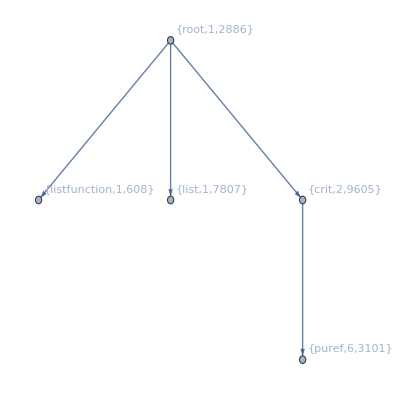

Select[Table[RandomInteger[10],RandomInteger[10]],1<RandomInteger[20]&]

```mathematica
DerivationGraphMutation[graphD_, rules_] :=
	Module[
		{element, parent, newDeriv, newElement, deleteVertices},
		element = RandomChoice[VertexList[graphD]];
		parent = First[Select[EdgeList[graphD], #[[2]] == element &]][[1]];
		newDeriv = RandomDerivation[element[[1]], rules, {start,0,0}, Graph[{}]];
		newDeriv = VertexDelete[newDeriv, First[Select[VertexList[newDeriv], VertexInDegree[newDeriv, #] == 0 &]]];
		newElement = First[Select[VertexList[newDeriv], VertexInDegree[newDeriv, #] == 0 &]];
		graphD2 = EdgeAdd[graphD, Join[EdgeList[newDeriv], {parent -> newElement}]];
		deleteVertices = 
			Flatten[NestWhileList[
				With[
					{currentNodes = #},
					Flatten[
						Map[
							With[
								{node = #},
								Select[node /. #& /@ EdgeRules[graphD2], ToString[#] ≠ ToString[node]&]
							]&,
							currentNodes
						], 
						1
					]
				]&,
				{element},
				Length[#] > 0 &
			],1];
		graphD2 = VertexDelete[graphD2, deleteVertices];
		graphD2
	]
	
resG = DerivationGraphMutation[graph, rules];
Head[resG]
Graph[resG, VertexLabels -> "Name"]
CodeFromDerivation[resG, rules]
```

## Derivation graph crossover

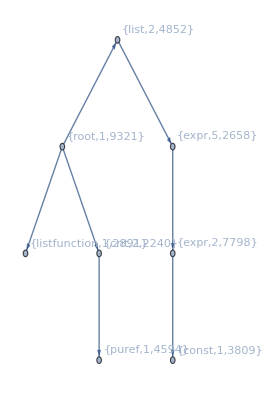

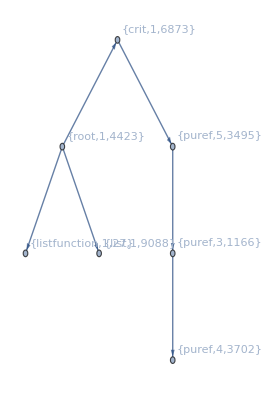

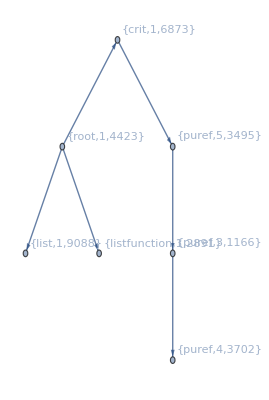

```mathematica
DerivationGraphCrossover[graph1_, graph2_] :=
	Module[
		{commonNodes, chosenNode, childGraph, common1, common2},
		commonNodes = 
			Select[
				VertexList[graph1],
				With[
					{node1 = #},
					Length[ 
						Select[
							VertexList[graph2],
							With[
								{node2 = #},
								node1[[1]] == node2[[1]] && node1[[2]] == node2[[2]]
							]&
						]
					] > 0
				]&
			];
		commonNodes = Select[commonNodes, ToString[#[[1]]] ≠ ToString[root] &];
		If[Length[commonNodes] == 0, Return[RandomChoice[{graph1, graph2}]]];
		chosenNode = RandomChoice[commonNodes];
		common1 = First[Select[VertexList[graph1], #[[1]] == chosenNode[[1]] && #[[2]] == chosenNode[[2]] &]];
		common2 = First[Select[VertexList[graph2], #[[1]] == chosenNode[[1]] && #[[2]] == chosenNode[[2]] &]];
		newBranch = 
			Subgraph[
				graph1,
				Flatten[
					NestWhileList[
						With[
							{currentNodes = #},
							Flatten[
								Map[
									With[
										{node = #},
										Select[node /. #& /@ EdgeRules[graph1], ToString[#] ≠ ToString[node]&]
									]&,
									currentNodes
								], 
								1
							]
						]&,
						{common1},
						Length[#] > 0 &
					],
				1]
			];
		childGraph = ReplaceDerivationSubgraph[graph2, newBranch, common2]
	]
	
g1 = RandomDerivation[root, rules, {start, 0, 0}, Graph[{}]];
g1 = VertexDelete[g1, First[Select[VertexList[g1], VertexInDegree[g1, #] == 0 &]]];
g2 = RandomDerivation[root, rules, {start, 0, 0}, Graph[{}]];
g2 = VertexDelete[g2, First[Select[VertexList[g2], VertexInDegree[g2, #] == 0 &]]];
Graph[g1, VertexLabels -> "Name"]
Graph[g2, VertexLabels -> "Name"]
child = DerivationGraphCrossover[g1, g2];
Graph[child, VertexLabels->"Name"]
```